# Graph Complexity

## コンセプト

ネットワークの規模を反映した複雑性指標であり、エッジによって連結されない部分があっても値を返す「直観的」な指標。

直観的とは、
1. |V|が多いほど複雑
2. |E|が多いほど複雑
3. 連結の様相が多様なほど複雑（エッジ数が同じであれば連結に偏りがあるほど複雑）

また、Vの集合に対して、
・連結されないVの集合に対して|V|を返す、同時に|V|を規定とする何らかのf(|V|,0)を満たす
・一重辺の連結による完全グラフ（自己ループを含む）では|V|を基底とする何らかのスケールf(|V|,1)を返す
・N多重辺の連結による完全グラフ（自己ループを含む）では|V|を基底とする何らかのスケールf(|V|,n)を返す

さらに、スケール（ノード数、エッジ数）をキャンセル可能な派生系を持つ

このような冗長性を反映する指標「Graph Redundancy Complexity」を開発する。

## Program

### Graph Union

GraphUnion[] は同一ノードペア間の複数エッジをreductionしてしまう。
GraphDisjointUnion[]はグラフ間のノードをIDが同じでもすべて異なるノードとして統一してしまう。

```mathematica
graphFederartion[g_,op___]:=Module[{v,e},
v=Union[Flatten[Map[VertexList,g]]];
e=Flatten[Map[EdgeList,g]];
Graph[v,e,op]
]
```

### Graph Redundancy Complexity

標準：スケールを考慮：f : f(|V|,n) = |V| E^n

```mathematica
graphRedundancyComplexityElement[g_Graph]:=Module[{vc,ec,ecmean,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
ecmean = ec/(vc^2);
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
{(vc),(E^ecmean),(E^etp),(vc) (E^ecmean) (E^etp)}
]
```

```mathematica
graphRedundancyComplexity[g_Graph]:=Module[{vc,ec,ecmean,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
ecmean = ec/(vc^2);
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
(vc) (E^ecmean) (E^etp)
]
```

スケールを考慮（Vが冪で効く）：f : f(|V|,n) = |V|^(n+1)

```mathematica
graphRedundancyComplexityP[g_Graph]:=Module[{vc,ec,ecmean,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
ecmean = ec/(vc^2);
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
(vc) (vc^ecmean) (E^etp)
]
```

Vスケールを考慮しない：

```mathematica
graphERedundancyComplexity[g_Graph]:=Module[{vc,ec,ecmean,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
ecmean = ec/(vc^2);
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
(E) (E^ecmean) (E^etp)
]
```

Eスケールを考慮しない：

```mathematica
graphVRedundancyComplexity[g_Graph]:=Module[{vc,ec,ecmean,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
ecmean = ec/(vc^2);
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
(vc) (vc^etp)
]
```

V,Eスケールを考慮しない：

```mathematica
graphNonRedundancyComplexity[g_Graph]:=Module[{vc,ec,ecmean,etp},
(*vc=VertexCount[g]//N;*)
(*ec=EdgeCount[g]//N;*)
(*ecmean = ec/(vc^2);*)
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
(E) (E) (E^etp)
]
```

### 指標以外で必要なプログラム

```mathematica
scaleEntropy[l_]:=Module[{mean},
mean=Mean[l];
Entropy[l]*mean
]
```

```mathematica
totalEntropy[l_]:=Module[{total},
total=Total[l];
total^Entropy[l]
]
```

```mathematica
fullCompleteGraph[n_,l_]:=AdjacencyGraph[Table[l,{n},{n}],DirectedEdges->True]
```

```mathematica
fullCompleteGraph[3,2]
```

-Graphics-

### その他考えた指標

```mathematica
graphComplexity[g_Graph]:=Module[{vc,ec,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vc^2 ec etp
]
```

```mathematica
graphComplexityE[g_Graph]:=Module[{vc,ec,etp},
vc=VertexCount[g]//N;
ec=EdgeCount[g]//N;
(*etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;*)
etp=Entropy[Map[#[[2]]&,Tally[EdgeList[g]]]]//N;
vc^2 ec etp
]
```

```mathematica
graphComplexityD[g_Graph]:=Module[{ec,etp,vc,vinetp,voutetp},
ec=EdgeCount[g]//N;
vc=VertexCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vinetp=Entropy[VertexInDegree[g]]//N;
voutetp=Entropy[VertexOutDegree[g]]//N;
ec etp vc vinetp vc voutetp
]
```

```mathematica
graphComplexityDp[g_Graph]:=Module[{ec,etp,vc,vinetp,voutetp},
ec=EdgeCount[g]//N;
vc=VertexCount[g]//N;
etp=Entropy[AdjacencyMatrix[g]//Flatten]//N;
vinetp=Entropy[VertexInDegree[g]]//N;
voutetp=Entropy[VertexOutDegree[g]]//N;
ec^etp vc^vinetp vc^voutetp
]
```

## Test

### Graph



```mathematica
g1=Graph[{1},{}]
```

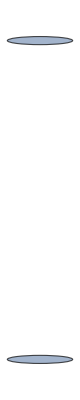

```mathematica
g2=Graph[{1,2},{}]
```

```mathematica
g3=Graph[{1,2,3},{}]
```

-Graphics-

```mathematica
gv0=Graph[{1,2,3},{}]
```

-Graphics-

```mathematica
gv1=AdjacencyGraph[ Table[1,{n,3},{n,3}] ,DirectedEdges->True]
```

-Graphics-

```mathematica
gv2=AdjacencyGraph[ Table[2,{n,3},{n,3}] ,DirectedEdges->True]
```

-Graphics-

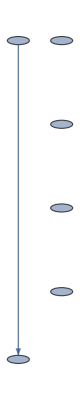

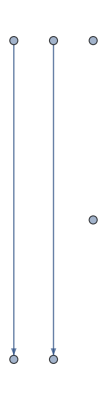

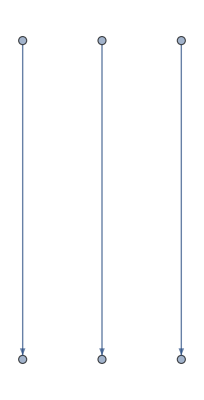

```mathematica
ge1=Graph[{1,2,3,4,5,6},{1->2}]
ge2=Graph[{1,2,3,4,5,6},{1->2,3->4}]
ge3=Graph[{1,2,3,4,5,6},{1->2,3->4,5->6}]
```

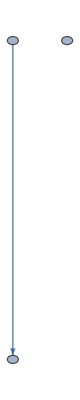

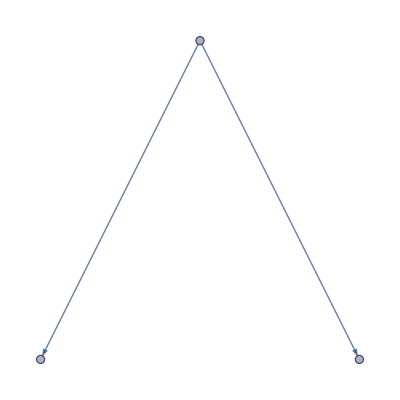

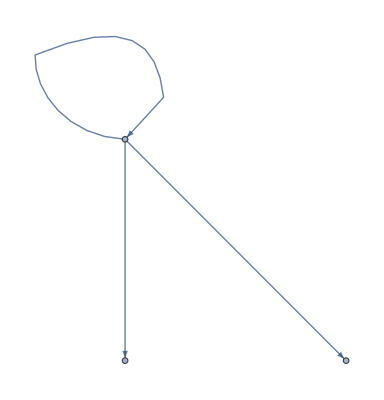

```mathematica
g11=Graph[{1,2,3},{1->2}]
g12=Graph[{1,2,3},{1->2,1->3}]
g13=Graph[{1,2,3},{1->2,1->3,1->1}]
```

```mathematica
cg1=CompleteGraph[4,DirectedEdges->True]
```

-Graphics-

```mathematica
fcg1=fullCompleteGraph[4,1]
```

-Graphics-

```mathematica
(gr1=CompleteGraph[6,DirectedEdges->True])//EdgeCount
```

30

```mathematica
gr2=Graph[Range[6],Table[RandomInteger[{1,6}]->RandomInteger[{1,6}],{30}]]
```

-Graphics-

```mathematica
(gr11=fullCompleteGraph[6,1])//EdgeCount
```

36

```mathematica
gr12=Graph[Range[6],Table[RandomInteger[{1,6}]->RandomInteger[{1,6}],{36}]]
```

-Graphics-

### Test of graphRedundancyComplexity

g1 = 1,  g2 = 2,  g3 = 3 を期待

```mathematica
{g1,graphRedundancyComplexity[g1]}
{g2,graphRedundancyComplexity[g2]}
{g3,graphRedundancyComplexity[g3]}
```

{-Graphics-,1.}

{-Graphics-,2.}

{-Graphics-,3.}

gv0 < gv1 < gv2  を期待

```mathematica
{gv0,graphRedundancyComplexity[gv0]}
{gv1,graphRedundancyComplexity[gv1]}
{gv2,graphRedundancyComplexity[gv2]}
```

{-Graphics-,3.}

{-Graphics-,8.15485}

{-Graphics-,22.1672}

ge1 < ge2 < ge3 を期待

```mathematica
{ge1,graphRedundancyComplexity[ge1]}
{ge2,graphRedundancyComplexity[ge2]}
{ge3,graphRedundancyComplexity[ge3]}
```

{-Graphics-,7.0039}

{-Graphics-,7.86069}

{-Graphics-,8.68788}

g11 < g12 < g13 を期待

```mathematica
{g11,graphRedundancyComplexity[g11]}
{g12,graphRedundancyComplexity[g12]}
{g13,graphRedundancyComplexity[g13]}
```

{-Graphics-,4.75195}

{-Graphics-,6.36326}

{-Graphics-,7.91263}

cg1 > fcg1, cg1 < fcg1 どちらでもよい

```mathematica
{{cg1,fcg1},{AdjacencyMatrix[cg1]//Normal,AdjacencyMatrix[fcg1]//Normal},{EdgeCount[cg1],EdgeCount[fcg1]},{graphRedundancyComplexity[cg1],graphRedundancyComplexity[fcg1]}}//TableForm
```

-Graphics- | -Graphics-
0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
12 | 16
14.8594 | 10.8731

gr1 < gr2 になりやすい

```mathematica
{{gr1,gr2},{VertexCount[gr1],VertexCount[gr2]},{EdgeCount[gr1],EdgeCount[gr2]},{graphRedundancyComplexity[gr1],graphRedundancyComplexity[gr2]}}//TableForm
```

-Graphics- | -Graphics-
6 | 6
30 | 30
21.664 | 45.1917

gr11 < gr12 を期待

```mathematica
{{gr11,gr12},{VertexCount[gr11],VertexCount[gr12]},{EdgeCount[gr11],EdgeCount[gr12]},{graphRedundancyComplexity[gr11],graphRedundancyComplexity[gr12]}}//TableForm
```

-Graphics- | -Graphics-
6 | 6
36 | 36
16.3097 | 52.7165

### Test of graphERedundancyComplexity

```mathematica
graphERedundancyComplexity[g1]
graphERedundancyComplexity[g2]
graphERedundancyComplexity[g3]
```

2.71828

2.71828

2.71828

gv0 < gv1 <  gv2  になる

```mathematica
graphERedundancyComplexity[gv0]
graphERedundancyComplexity[gv1]
graphERedundancyComplexity[gv2]
```

2.71828

7.38906

20.0855

ge1 < ge2 < ge3 を期待

```mathematica
graphERedundancyComplexity[ge1]
graphERedundancyComplexity[ge2]
graphERedundancyComplexity[ge3]
```

3.1731

3.56126

3.93602

g11 < g12 < g13 を期待

```mathematica
graphERedundancyComplexity[g11]
graphERedundancyComplexity[g12]
graphERedundancyComplexity[g13]
```

4.30571

5.76571

7.16958

cg1 > fcg1, cg1 < fcg1 どちらでもよい

```mathematica
{{cg1,fcg1},{AdjacencyMatrix[cg1]//Normal,AdjacencyMatrix[fcg1]//Normal},{EdgeCount[cg1],EdgeCount[fcg1]},{graphERedundancyComplexity[cg1],graphERedundancyComplexity[fcg1]}}//TableForm
```

-Graphics- | -Graphics-
0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
12 | 16
10.098 | 7.38906

gr1 < gr2 になりやすいはず

```mathematica
{{gr1,gr2},{EdgeCount[gr1],EdgeCount[gr2]},{graphERedundancyComplexity[gr1],graphERedundancyComplexity[gr2]}}//TableForm
```

-Graphics- | -Graphics-
30 | 30
9.81483 | 20.474

gr11 < gr12 になるはず

```mathematica
{{gr11,gr12},{EdgeCount[gr11],EdgeCount[gr12]},{graphERedundancyComplexity[gr11],graphERedundancyComplexity[gr12]}}//TableForm
```

-Graphics- | -Graphics-
36 | 36
7.38906 | 23.883

### Test of graphVRedundancyComplexity

```mathematica
graphVRedundancyComplexity[g1]
graphVRedundancyComplexity[g2]
graphVRedundancyComplexity[g3]
```

1.

2.

3.

同じ値になる

```mathematica
graphVRedundancyComplexity[gv0]
graphVRedundancyComplexity[gv1]
graphVRedundancyComplexity[gv2]
```

3.

3.

3.

ge1 < ge2 < ge3 を期待

```mathematica
graphVRedundancyComplexity[ge1]
graphVRedundancyComplexity[ge2]
graphVRedundancyComplexity[ge3]
```

7.53221

8.81274

10.0312

g11 < g12 < g13 を期待

```mathematica
graphVRedundancyComplexity[g11]
graphVRedundancyComplexity[g12]
graphVRedundancyComplexity[g13]
```

4.40105

5.36853

6.03692

cg1 > fcg1, cg1 < fcg1 どちらでもよい

```mathematica
{{cg1,fcg1},{AdjacencyMatrix[cg1]//Normal,AdjacencyMatrix[fcg1]//Normal},{EdgeCount[cg1],EdgeCount[fcg1]},{graphVRedundancyComplexity[cg1],graphVRedundancyComplexity[fcg1]}}//TableForm
```

-Graphics- | -Graphics-
0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
12 | 16
8.72207 | 4.

gr1 < gr2 になりやすいはず

```mathematica
{{gr1,gr2},{EdgeCount[gr1],EdgeCount[gr2]},{graphVRedundancyComplexity[gr1],graphVRedundancyComplexity[gr2]}}//TableForm
```

-Graphics- | -Graphics-
30 | 30
13.451 | 50.2226

gr11 < gr12 になるはず

```mathematica
{{gr11,gr12},{EdgeCount[gr11],EdgeCount[gr12]},{graphVRedundancyComplexity[gr11],graphVRedundancyComplexity[gr12]}}//TableForm
```

-Graphics- | -Graphics-
36 | 36
6. | 49.0969

### Test of graphNonRedundancyComplexity

```mathematica
graphNonRedundancyComplexity[g1]
graphNonRedundancyComplexity[g2]
graphNonRedundancyComplexity[g3]
```

7.38906

7.38906

7.38906

gv0 =  gv1 =  gv2  になる

```mathematica
graphNonRedundancyComplexity[gv0]
graphNonRedundancyComplexity[gv1]
graphNonRedundancyComplexity[gv2]
```

7.38906

7.38906

7.38906

ge1 < ge2 < ge3 を期待

```mathematica
graphNonRedundancyComplexity[ge1]
graphNonRedundancyComplexity[ge2]
graphNonRedundancyComplexity[ge3]
```

8.38908

9.15737

9.84374

g11 < g12 < g13 を期待

```mathematica
graphNonRedundancyComplexity[g11]
graphNonRedundancyComplexity[g12]
graphNonRedundancyComplexity[g13]
```

10.4733

12.5498

13.9644

cg1 > fcg1, cg1 < fcg1 どちらでもよい

```mathematica
{{cg1,fcg1},{AdjacencyMatrix[cg1]//Normal,AdjacencyMatrix[fcg1]//Normal},{EdgeCount[cg1],EdgeCount[fcg1]},{graphNonRedundancyComplexity[cg1],graphNonRedundancyComplexity[fcg1]}}//TableForm
```

-Graphics- | -Graphics-
0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
12 | 16
12.9661 | 7.38906

gr1 < gr2 になりやすいはず

```mathematica
{{gr1,gr2},{EdgeCount[gr1],EdgeCount[gr2]},{graphNonRedundancyComplexity[gr1],graphNonRedundancyComplexity[gr2]}}//TableForm
```

-Graphics- | -Graphics-
30 | 30
11.5949 | 24.1871

gr11 < gr12 になるはず

```mathematica
{{gr11,gr12},{EdgeCount[gr11],EdgeCount[gr12]},{graphNonRedundancyComplexity[gr11],graphNonRedundancyComplexity[gr12]}}//TableForm
```

-Graphics- | -Graphics-
36 | 36
7.38906 | 23.883

### Compare

entropy

```mathematica
scaleEntropy[{0,0,0,1}]//N
scaleEntropy[{1,1,0,1}]//N
scaleEntropy[{0,0,0,1,0}]//N
```

0.140584

0.421751

0.10008

```mathematica
totalEntropy[{0,0,0,1}]//N
totalEntropy[{1,1,0,1}]//N
totalEntropy[{0,0,0,1,0}]//N
```

1.

1.85482

1.

## Memo